{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>],z→InterpolatingFunction[{{0.,200.}},<>]}}

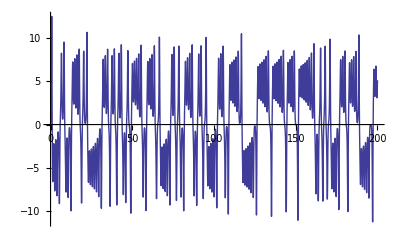

-Graphics3D-

-Graphics3D-

InterpolatingFunction::dmval: Input value {-12.4401} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-84.3707} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot :: cvmit will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-132.199} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

-Graphics3D-

-Graphics3D-

```mathematica
mysol=NDSolve[{x'[t]==-3 (x[t]-y[t]),y'[t]==-x[t] z[t]+26.5 x[t]-y[t],z'[t]==x[t] y[t]-z[t],x[0]==z[0]==0,y[0]==1},{x,y,z},{t,0,200},MaxSteps->100000] 
myx[t_]:=Evaluate[x[t]/.mysol];myplot=Plot[myx[t],{t,0,200}] 
pp1=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.mysol],{t,0,200},AxesLabel->{"x","y","z"},PlotPoints->150] 

cp1=ContourPlot3D[x==10,{x,-20,20},{y,-20,20},{z,0,50},Mesh->None,ContourStyle->{LightPurple,Opacity[0.4]}] (*get line segments from plot*) 
pts=Cases[myplot,Line[{t__}]->t,∞];
(*from set above,select all pairs which exhibit a sign change to\ identify a root*)myselection=Select[Split[pts,Sign[Last[#2]]==-Sign[Last[#1]]&],Length[#1]==2&];
(*get first element of the array*)
mymap=Map[First,myselection,{2}];(*find in line segments where each changes sign*)mymap2=Map[FindRoot[myx[t]==10,{t,#[[1]],#[[2]]}]&,mymap];
mypoints=t/.mymap2;
(*plot Poincare map where x[t]=0*)myplots=Point@{First[Evaluate[x[#]/.mysol]],First[Evaluate[y[#]/.mysol]],First[Evaluate[z[#]/.mysol]]}&/@mypoints;sg1=Show[Graphics3D[{Red,PointSize[0.05],myplots}]] (*show everything*) 
Show[{pp1,cp1,sg1}]
```